```mathematica
SetDirectory["/home/nuno/AulasFC/projeto3/solution/"];
```

#### 1b

```mathematica
t={30,60.01,90};
For[i=1,i≤Length[t],i++,
a = Import[StringJoin["1b/out_",ToString[t[[i]]],"s.txt"],"Table"];
fig1=ListPlot3D[a,PlotRange->All,AxesLabel->{"x (m)"  ,"y (m)","T (.baK)"}];
Print[fig1];
Export[StringJoin["1b/sol_",ToString[t[[i]]],"s.pdf"],fig1,"PDF"];
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

#### 2b

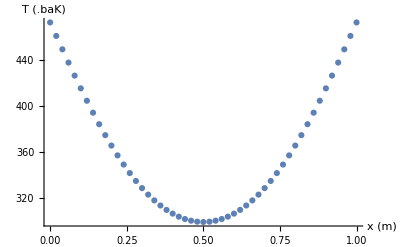

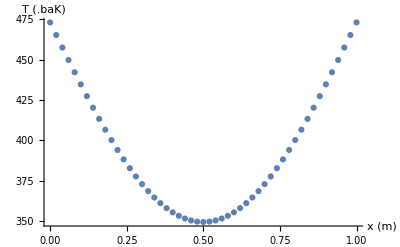

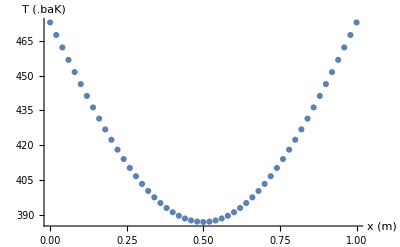

```mathematica
t={30,60.01,90};
For[i=1,i≤Length[t],i++,
a = Import[StringJoin["2b/out_",ToString[t[[i]]],"s.txt"],"Table"];
fig1=ListPlot[a,PlotRange->All,AxesLabel->{"x (m)"  ,"T (.baK)"}];
Print[fig1];
Export[StringJoin["2b/sol_",ToString[t[[i]]],"s.pdf"],fig1,"PDF"];
]
```

#### 2c

```mathematica
t={30,60.01,90};
For[i=1,i≤Length[t],i++,
a = Import[StringJoin["2c/out_",ToString[t[[i]]],"s.txt"],"Table"];
fig1=ListPlot3D[a,PlotRange->All,AxesLabel->{"x (m)"  ,"y (m)","T (.baK)"}];
Print[fig1];
Export[StringJoin["2c/sol_",ToString[t[[i]]],"s.pdf"],fig1,"PDF"];
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-